```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\flux_pmf\xin\PVP5\111Ag\short_40_windows_US\1_start\1.5ns\k_0.7\ui_nostat\data

```mathematica
data=Table[i,{i,40}];
```

```mathematica
For[i=1,i≤1,i++,
log=OpenRead["1"];
temp=ReadList[log,{Number,Number,Number}];
Close[log];
data[[i]]=temp;
]
```

```mathematica
Length[data[[1]]]
```

100000

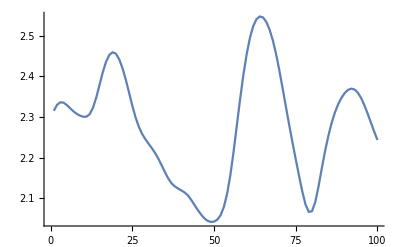

```mathematica
ListLinePlot[data[[1,1;;100,1]]]
```

```mathematica
AutocorrelationTest[data[[1,1;;400;;10,1]]]
```

0.158486

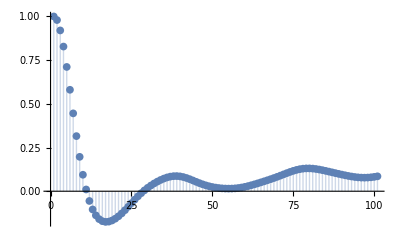

```mathematica
ListPlot[CorrelationFunction[data[[1,1;;-1,1]],{100}],Filling->Axis,PlotRange->All]
```